## Importing Data

Link to CSV documentation.

Import superfunction to get data into Mathematica.

Export export data (pdf, png, ...) for other programs to use.

### Mockup data and Interpolation function

```mathematica
data=Table[{"ID", RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}], RandomInteger[{1,255}],i},{i,0,100}];
```

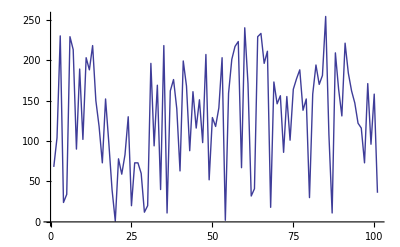

```mathematica
lp=ListPlot[data[[All,7]],Joined->True]
```

```mathematica
fun=Interpolation[data[[All,7]]]
```

InterpolatingFunction[{{1,101}},<>]

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

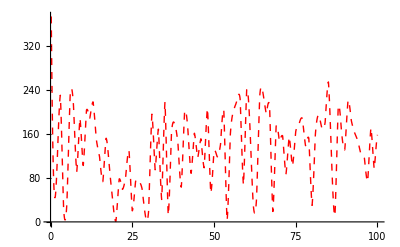

```mathematica
pl=Plot[fun[t],{t,0,100},PlotStyle->{Red,Dashed}]
```

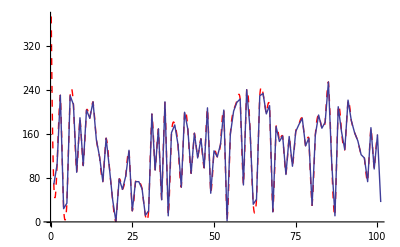

```mathematica
Show[pl,lp]
```

```mathematica
derfun=D[fun]
```

InterpolatingFunction[{{1,101}},<>]

```mathematica
derfun[10]
```

102

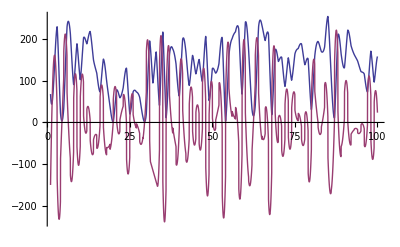

```mathematica
Plot[Evaluate@{fun[x],D[fun[x],x]},{x,1,100}]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

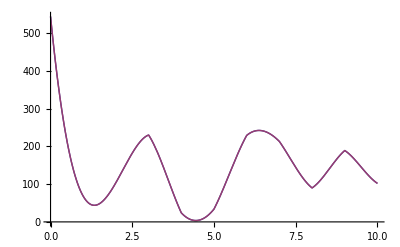

```mathematica
Plot[{derfun[x],},{x,0,10}]
```

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
NDSolve
```

## Organizing data

```mathematica
Cases
```

```mathematica
Select
```

```mathematica
GatherBy
```

Example of GatherBy:

```mathematica
gatherdata=Transpose@{RandomChoice[{a,b},5],RandomInteger[10,5]}
```

{{a,1},{b,3},{a,1},{b,6},{a,0}}

```mathematica
GatherBy[gatherdata,First]
```

{{{a,1},{a,1},{a,0}},{{b,3},{b,6}}}

## Interactivity

Generate a sinusoid with some random noise added:

```mathematica
sinData=Table[Sin[x]+0.1 RandomVariate[NormalDistribution[0,1]],{x,0,10,0.1}];
```

Plot it:

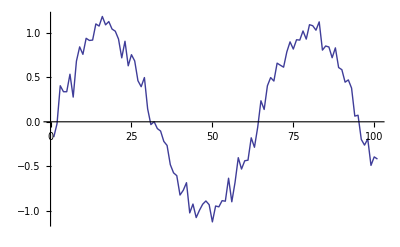

```mathematica
ListPlot[sinData,Joined->True]
```

Create a small “app” that runs a LowpassFilter on the data:

```mathematica
Manipulate[ListPlot[LowpassFilter[sinData,var],Joined->True,PlotRange->{-2,2}],{var,0,π,π/10}]
```

```mathematica
NotebookDirectory[]
```

/Users/johanr/WolframWorkspaces/Base/johanr/Proto/StudentCompetitions/